```mathematica
(****************ALPHA DECAY HALF LIFE USING BASS-80 NUCLEAR POTENTIAL************************************************)
```

```mathematica
hbar=1.054571800*10^(-34); (* h bar*)

evconvert=1.60218*10^-19;   (* one electron volt = 1.6 * 10^-19 joules*)

mp=1.6726219*10^(-27);   (*mass of proton*)

r0=1.20*(10^(-15));  (*radius constant*)

factor=9*10^9;

mn=1.6749*10^-27;  

mu=((A1*A2)/(A1+A2))*mn;

factor1=((1/hbar)*(2*mu)^(1/2));

e=1.60217662*10^(-19);

pi=3.14;

fermi=10^(-15);

MeV=(10^(6)*evconvert);

Z1=116;
A1=290;
Z2=2;  
A2=4;

Qval=11.81

Q=Qval*MeV

A=A1+A2;
Z=Z1+Z2;
N1=A1-Z1;
N2=A2-Z2;

I1=((N1-Z1)/A1);

I2=((N2-Z2)/A2);
```

11.81

1.89217×10^-12

```mathematica
(**************** Sharp radius and Central radii************************************************)

RS1=(1.28*(A1^(1/3))+0.8*(A1^(-1/3))-0.76)

RS2=(1.28*(A2^(1/3))+0.8*(A2^(-1/3))-0.76)


RS0=(1.28*(A^(1/3))+0.8*(A^(-1/3))-0.76)



R1=(RS1-((0.98)/RS1))*fermi;
R2=(RS2-((0.98)/RS2))*fermi;

Rdash=((R1*R2)/(R1+R2));

R=(RS1+RS2)*fermi;
```

7.83332

1.77584

7.87154

```mathematica
(**************** Nuclear Potential (Reference - Nuclear Physics A ,934,(2015) 110–120)************************************************)
```

```mathematica
A0=0.033*(fermi/MeV);
B0=0.007*(fermi/MeV);
d1=3.5*fermi;
d2=0.65*fermi;

phi[r_]:=(1/(A0* Exp[((r-R1-R2)/d1)]+B0* Exp[(r-R1-R2)/d2]))

Vn[r_]:=(-1)*Rdash * phi[r]

(****************Coloumb Potential************************************************)
```

```mathematica
term1=Z1*Z2*(e^2)*(1/r);

term2=Z1*Z2*(e^2)*(1/R)*(1/2)*(3-((r^2)/(R^2)))

Vc[r_]=Piecewise[{ {factor*(term1),   R<r},{factor*term2,r <=R}}  ]
```

3.0988×10^-22 (3-1.083×10^28 r^2)

Piecewise[{{(5.35983×10^-26)/r, 9.60916×10^-15<r}, {2.78892×10^-12 (3-1.083×10^28 r^2), r≤9.60916×10^-15}, {0, True}}]

```mathematica
(****************Centrifugal potential************************************************)
l=0;
```

```mathematica
VL[r_]=((l+1/2)^(2))*(hbar*hbar)*(1/2)*(1/(mu*r*r));
```

```mathematica
(****************Total Potential************************************************)
```

```mathematica
V[r_]=Vn[r]+Vc[r]+VL[r]
```

-(1.05627×10^-15)/(0.000205969 ⅇ^(2.85714×10^14 (-8.9322×10^-15+r))+0.0000436905 ⅇ^(1.53846×10^15 (-8.9322×10^-15+r)))+(2.1036×10^-43)/r^2+(Piecewise[{{(5.35983×10^-26)/r, 9.60916×10^-15<r}, {2.78892×10^-12 (3-1.083×10^28 r^2), r≤9.60916×10^-15}, {0, True}}])

```mathematica
rb= factor*Z1*Z2*(e^2)*(1/Q)
```

2.83263×10^-14

```mathematica
s1=Plot[Vc[r]/MeV,{r,0, rb},ImageSize->900, PlotStyle->Red];
s2=Plot[Vn[r]/MeV,{r,0, rb},ImageSize->900 ,PlotStyle->Blue];
s3=Plot[VL[r]/MeV,{r,0,rb},ImageSize->900 ,PlotStyle-> Yellow];
s4=Plot[V[r]/MeV,{r,0, rb},ImageSize->900,PlotStyle-> Green];
s5=Plot[Q/MeV,{r,0,rb},ImageSize->900,PlotStyle-> Cyan];
```

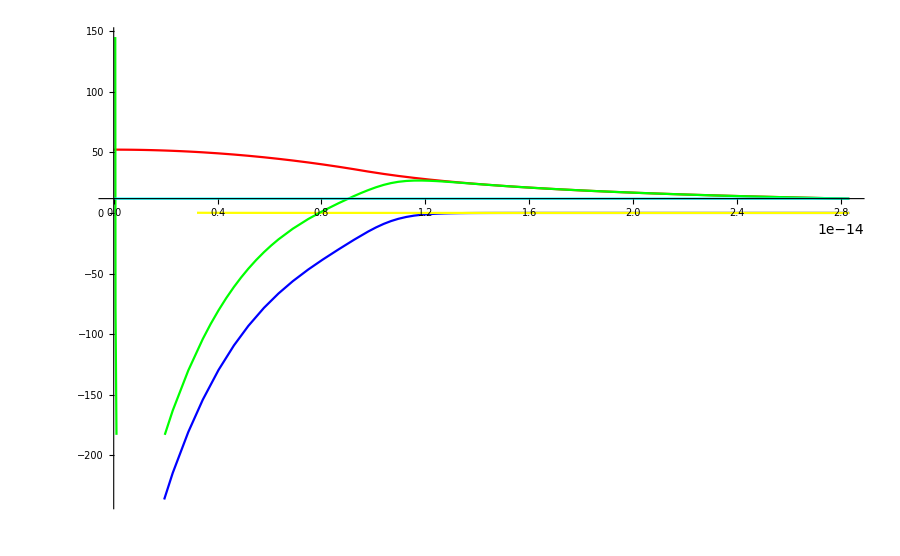

```mathematica
Show[{s1,s2,s3,s4,s5},PlotRange-> Automatic]
```

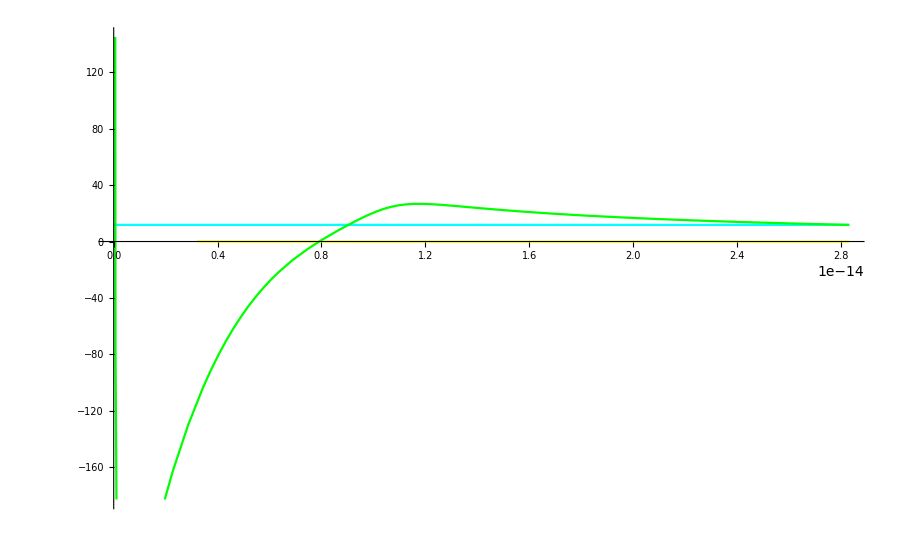

```mathematica
Show[{s5,s3,s4}, PlotRange->Automatic]
```

```mathematica
(****************Turning Points & Tunneling Probability************************************************)
```

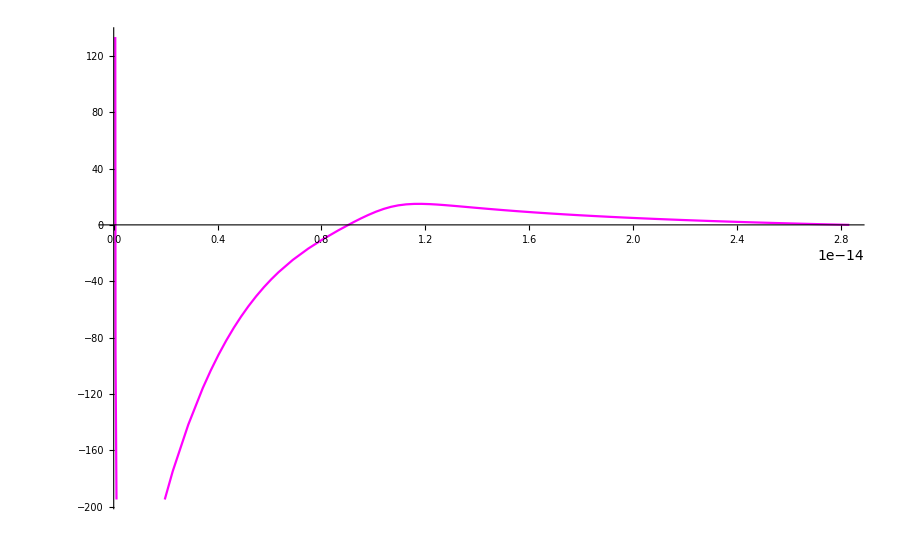

```mathematica
Plot[(V[r]-Q)/MeV,{r,0, rb},ImageSize->900,PlotStyle-> Magenta]
```

```mathematica
r1=r/.FindRoot[(Q-V[r])*10^(10), {r,(5*10^(-15))}, Method->"Newton"]
r2=r/.FindRoot[(Q-V[r])*10^(10), {r,(7*10^(-15)), 1*10^-14}]
r3=r/.FindRoot[(Q-V[r])*10^(10), {r,(2.35*10^(-14))}]
```

9.03216×10^-15

9.03519×10^-15

2.83063×10^-14

```mathematica
K=factor1*NIntegrate[(V[r]-Q)^(1/2),{r,r2,r3}]
```

19.5927

```mathematica
P=Exp[-2K]
```

9.59394×10^-18

```mathematica
(****************PREFORMATION FACTOR OF ALPHA (Reference - Braz J Phys (2016) 46:355–360) ************************************************)
BEparent= 7080*A*0.001           (*PUT in kev*)
BEdaughter=7120 * A1*0.001
BE1= 7097   *(A-1)*0.001         (*Z-1,A-1*)
BE2=7077  *(A-1)*0.001              (*Z,A-1*)
BEalpha=28.3;

Qval=BEdaughter+BEalpha-BEparent
```

2081.52

2064.8

2079.42

2073.56

11.58

```mathematica
Etot=(BEparent-BEdaughter)*1000

Ef=(3*BEparent+ BEdaughter-2*BE1-2*BE2)*1000

Salpha=(Ef/Etot)
```

16720.

3396.

0.20311

```mathematica
(****************HALF LIFE, classical frequency************************************************)

freq=((2*Q*(1/mu))^(1/2))*(1/(2R))

lambda=  freq* P*Salpha
```

1.24518×10^21

2426.38

```mathematica
T=0.693/lambda
```

0.000285611

```mathematica
Log10[T]
```

-3.54423

```mathematica
(****************HALF LIFE, frequency quantum mechanics formula************************************************)
```

```mathematica
Ev=Q*(0.056+0.039*Exp[(4-A2)/2.5]);

freq=((2* Ev)/(hbar*3.14*2))
```

5.42849×10^20

```mathematica
lambda=  freq* P*Salpha
```

1057.81

```mathematica
T=0.693/lambda
```

0.000655127

```mathematica
Log10[T]
```

-3.18367